```mathematica
<<"C:\\Users\\aliha\\Desktop\\UNET\\UNET_modified.m";
dirimg="C:\\Users\\aliha\\Downloads\\fabrice-ali\\deeplearning\\data\\train\\train_images_8bit"; 
dirmasks="C:\\Users\\aliha\\Downloads\\fabrice-ali\\deeplearning\\data\\train\\train_masks";
```

```mathematica
{X,Y}=dataPrep[dirimg,dirmasks];
```

```mathematica
nNet=UNET
```

NetGraph[<>]

```mathematica
nNetInfo=trainNet[nNet,X[[;;300]],Y[[;;300]]]
```

NetTrainResultsObject[<>]

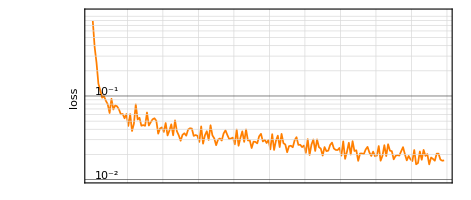

```mathematica
nNetInfo["LossEvolutionPlot"]
```

```mathematica
nNetTrained=nNetInfo["TrainedNet"]
```

NetGraph[<>]

```mathematica
generateImage[]:=With[{imgs=Thread[{X[[301;;]],Y[[301;;]]}]},
MapAt[NetDecoder[{"Image"}],RandomChoice@imgs,2]
]
```

```mathematica
{img,ground}=generateImage[]
```

{-Graphics-,-Graphics-}

```mathematica
{img,#,ground,HighlightImage[img,MorphologicalPerimeter@Binarize@#]}&[NetDecoder[{"Image"}]@nNetTrained[img,TargetDevice-> "GPU"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
measureModelAccuracy[nNetTrained,X[[301;;]],Y[[301;;]] ]
```

{0.986467,1 | 0.992969
2 | 0.995898
3 | 0.991445
4 | 0.98832
5 | 0.991875
6 | 0.991289
7 | 0.988672
8 | 0.99168
9 | 0.981797
10 | 0.987969
11 | 0.980039
12 | 0.98668
13 | 0.984883
14 | 0.979844
15 | 0.981797
16 | 0.971133
17 | 0.972891
18 | 0.979531
19 | 0.978008
20 | 0.967539
21 | 0.986875
22 | 0.970938
23 | 0.985469
24 | 0.988242
25 | 0.986133
26 | 0.985664
27 | 0.988125
28 | 0.990625
29 | 0.988281
30 | 0.988516
31 | 0.988984
32 | 0.988125
33 | 0.99082
34 | 0.987773
35 | 0.990078
36 | 0.983125
37 | 0.983398
38 | 0.986367
39 | 0.98293
40 | 0.988438
41 | 0.993398
42 | 0.991055
43 | 0.986719
44 | 0.987734
45 | 0.990781
46 | 0.990508
47 | 0.992852
48 | 0.991758
49 | 0.994023
50 | 0.988086
51 | 0.993633
52 | 0.990703
53 | 0.991602
54 | 0.985664
55 | 0.987695
56 | 0.986016
57 | 0.993828
58 | 0.987344
59 | 0.980977
60 | 0.985117
61 | 0.985156
62 | 0.987578
63 | 0.983477
64 | 0.987031
65 | 0.980586
66 | 0.984297
67 | 0.987578
68 | 0.994063
69 | 0.982617
70 | 0.985664
71 | 0.98375
72 | 0.983594
73 | 0.987227
74 | 0.981797
75 | 0.98082
76 | 0.975039
77 | 0.98207
78 | 0.978281
79 | 0.996055
80 | 0.982148
81 | 0.986758
82 | 0.98707
83 | 0.989375
84 | 0.987891
85 | 0.984688
86 | 0.986758
87 | 0.993281
88 | 0.9925
89 | 0.991016
90 | 0.991172}

```mathematica
saveNeuralNet[nNetTrained]
```

C:\Users\aliha\Desktop\UNET\unet.wlnet